## Исходные данные

### Рандомные

```mathematica
data1 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\traj___1.txt","Table"];
data2 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\traj___2.txt","Table"];
data3 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\traj___3.txt","Table"];
data4 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\traj___4.txt","Table"];
l1=ListPointPlot3D[data1,PlotStyle->Hue[0.1]];
l2=ListPointPlot3D[data2,PlotStyle->Hue[0.3]];
l3=ListPointPlot3D[data3,PlotStyle->Hue[0.5]];
l4=ListPointPlot3D[data4,PlotStyle->Hue[0.7]];
Show[l1,l2,l3,l4,PlotRange->Full]
```

-Graphics3D-

### Точное решение

```mathematica
data1n201 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj1_201.txt","Table"];
data1n401 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj1_401.txt","Table"];
data1n801 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj1_801.txt","Table"];
data1n1601 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj1_1601.txt","Table"];
data1n3201 = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj1_3201.txt","Table"];
data1Exact = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj1.txt","Table"];
data2Exact = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj2.txt","Table"];
data3Exact = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj3.txt","Table"];
data4Exact = Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Параллели\\N_body_mpi\\Точность\\traj4.txt","Table"];
dataEx1=Table[Delete[data1Exact[[i]],1],{i,1,Length[data1Exact]}];
dataEx2=Table[Delete[data2Exact[[i]],1],{i,1,Length[data2Exact]}];
dataEx3=Table[Delete[data3Exact[[i]],1],{i,1,Length[data3Exact]}];
dataEx4=Table[Delete[data4Exact[[i]],1],{i,1,Length[data4Exact]}];
```

```mathematica
lEx1=ListPointPlot3D[dataEx1,PlotStyle->Hue[0.2]];
lEx2=ListPointPlot3D[dataEx2,PlotStyle->Hue[0.4]];
lEx3=ListPointPlot3D[dataEx3,PlotStyle->Hue[0.6]];
lEx4=ListPointPlot3D[dataEx4,PlotStyle->Hue[0.8]];
Show[lEx1,lEx2,lEx3,lEx4,PlotRange->Full]
```

-Graphics3D-

-Graphics3D-

## Порядок

```mathematica
Error201 = Table[√((data1n201[[i]][[1]]-dataEx1[[i]][[1]])^2+(data1n201[[i]][[2]]-dataEx1[[i]][[2]])^2+(data1n201[[i]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Error401=Table[√((data1n401[[(i-1)*2+1]][[1]]-dataEx1[[i]][[1]])^2+(data1n401[[(i-1)*2+1]][[2]]-dataEx1[[i]][[2]])^2+(data1n401[[(i-1)*2+1]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Error801=Table[√((data1n801[[(i-1)*4+1]][[1]]-dataEx1[[i]][[1]])^2+(data1n801[[(i-1)*4+1]][[2]]-dataEx1[[i]][[2]])^2+(data1n801[[(i-1)*4+1]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Error1601=Table[√((data1n1601[[(i-1)*8+1]][[1]]-dataEx1[[i]][[1]])^2+(data1n1601[[(i-1)*8+1]][[2]]-dataEx1[[i]][[2]])^2+(data1n1601[[(i-1)*8+1]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Error3201=Table[√((data1n3201[[(i-1)*16+1]][[1]]-dataEx1[[i]][[1]])^2+(data1n3201[[(i-1)*16+1]][[2]]-dataEx1[[i]][[2]])^2+(data1n3201[[(i-1)*16+1]][[3]]-dataEx1[[i]][[3]])^2),{i,1,Length[dataEx1]}];
Total[Error201]
Total[Error401]
Total[Error1601]
Total[Error3201]
```

2.01126

0.530122

0.0343582

0.00853476

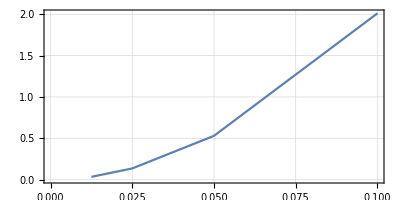

```mathematica
ListLinePlot[{{0.1,Total[Error201]},{0.05,Total[Error401]},{0.025,Total[Error801]},{0.0125,Total[Error1601]}},PlotTheme->"Detailed",AspectRatio->1/2]
```

```mathematica
Grid[{{tau,0.1,0.05,0.025,0.0125,0.00625},{p^n,,Total[Error201]/Total[Error401],Total[Error401]/Total[Error801],Total[Error801]/Total[Error1601],Total[Error1601]/Total[Error3201]}},Frame->All]
```

tau | 0.1 | 0.05 | 0.025 | 0.0125 | 0.00625
p^n |  | 3.79396 | 3.89672 | 3.95955 | 4.02568

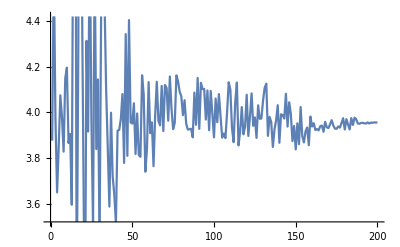

```mathematica
ListLinePlot[Table[Error801[[i]]/Error1601[[i]],{i,2,Length[Error201]}]]
```

## Ускорения

### M = 10000, N = 10, T = 20

```mathematica
d1 = {{8,0.519004/0.0697611},{16,0.519004/0.0404292},{24,0.519004/0.0248525},{32,0.519004/0.0217806},{40,0.519004/0.0177211},{48,0.519004/0.0160384},{56,0.519004/0.0151387},{64,0.519004/0.013893}}//N
```

{{8.,7.43973},{16.,12.8374},{24.,20.8834},{32.,23.8287},{40.,29.2873},{48.,32.3601},{56.,34.2833},{64.,37.3572}}

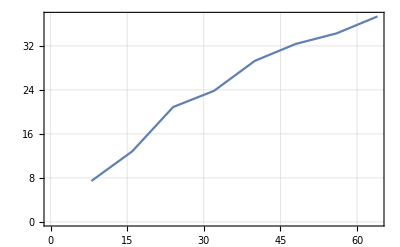

```mathematica
l1 = ListLinePlot[d1,PlotTheme->"Detailed"]
```

### Уменьшен объем пересылаемых данных: M = 10000, N = 10, T = 20

```mathematica
d2 = {{8,0.503574/0.0681037},{16,0.503574/0.0390863},{24,0.503574/0.0238642},{32,0.503574/0.0212277},{40,0.503574/0.0163332},{48,0.503574/0.0152333},{56,0.503574/0.0139979},{64,0.503574/0.0119772}}//N
```

{{8.,7.39422},{16.,12.8836},{24.,21.1017},{32.,23.7225},{40.,30.8313},{48.,33.0574},{56.,35.975},{64.,42.0444}}

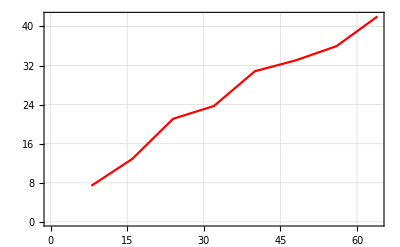

```mathematica
l2 = ListLinePlot[d2,PlotTheme->"Detailed",PlotStyle->Red]
```

### Нормальное ускорение

```mathematica
d3 = {{8,0.502758/0.0687855},{16,0.502758/0.0398648},{24,0.502758/0.0243097},{32,0.502758/0.0223096},{40,0.502758/0.0162294},{48,0.502758/0.015331},{56,0.502758/0.0131842},{64,0.502758/0.0107181}}//N
```

{{8.,7.30907},{16.,12.6116},{24.,20.6814},{32.,22.5355},{40.,30.9782},{48.,32.7936},{56.,38.1334},{64.,46.9074}}

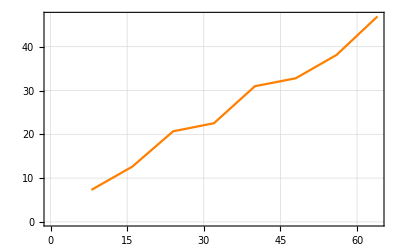

```mathematica
l3 = ListLinePlot[d3,PlotTheme->"Detailed",PlotStyle->Orange]
```

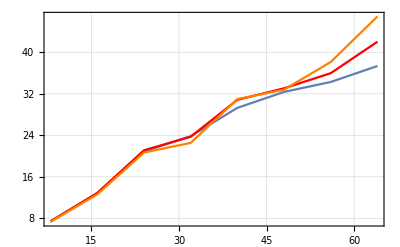

```mathematica
Show[l1,l2,l3,PlotRange->All]
```

### M = 20000, N = 10, T = 20

```mathematica
d3 = {{8,2.27841/0.30981},{16,2.27841/0.217965},{24,2.27841/0.118444},{32,2.27841/0.110229},{40,2.27841/0.0802254},{48,2.27841/0.0749531},{56,2.27841/0.0610033},{64,2.27841/0.0561243}};
```

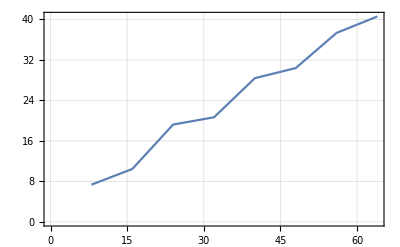

```mathematica
l3 = ListLinePlot[d3,PlotTheme->"Detailed"]
```